```mathematica
data=Table[Random[],{100}]//Sort
```

{0.00411987,0.0100695,0.0142709,0.0301791,0.0324122,0.0424199,0.0429911,0.0448933,0.0549628,0.0616374,0.0737501,0.0850625,0.0878844,0.0906365,0.0947563,0.101349,0.102781,0.129628,0.138895,0.142847,0.156394,0.164782,0.177093,0.17902,0.194032,0.200733,0.212645,0.229669,0.230977,0.23805,0.241456,0.264556,0.272874,0.280548,0.283639,0.300956,0.303025,0.309454,0.309919,0.338453,0.343376,0.348783,0.371092,0.384998,0.402833,0.404315,0.412902,0.42509,0.432106,0.443081,0.446735,0.451564,0.455829,0.467865,0.477468,0.487393,0.497733,0.497852,0.521658,0.526513,0.527485,0.529425,0.540882,0.544567,0.560467,0.562514,0.574475,0.588746,0.590459,0.59406,0.594926,0.610712,0.637174,0.643124,0.656488,0.690452,0.71101,0.758552,0.768942,0.772019,0.790112,0.801681,0.803104,0.810088,0.818415,0.83245,0.859748,0.889565,0.895551,0.897605,0.902048,0.907393,0.910946,0.937571,0.940262,0.948043,0.966407,0.971001,0.986186,0.990306}

```mathematica
(*请以上述表单为间断点，构造实数域上的分段常值函数，逐段取值分别为0..100，即整体单调增*)
```

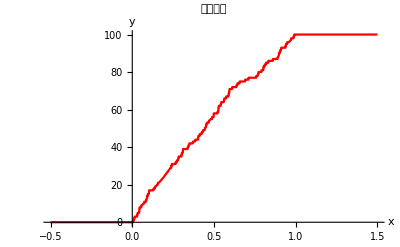

```mathematica
list={{0,x≤Indexed[data ,1]}};
For[i=1,i<100,i++,
AppendTo[list,{i,Indexed[data,(i)]<x≤Indexed[data,i+1]}]
];
AppendTo[list,{100,Indexed[data,100]<x}];
func=Piecewise[list];
Plot[func,{x,-0.5,1.5},PlotStyle->RGBColor[1,0,0],AxesLabel->{"x","y"},PlotLabel->("分段函数")]
```